```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/deddu/Documents/workspace/MLtests/misc

```mathematica
"."
```

.

```mathematica
d=Reverse[Flatten[Import["stats.tsv"]]];
```

```mathematica
d2=Reverse[Flatten[Import["smarts_stats_10.tsv"]]];
```

```mathematica
zipfdata=Table[{i,(d/10000)⟦i⟧},{i,Length[d]}];
```

```mathematica
zipfmodel=1/(x^s ∑_(n=1)^Length[d] 1/n^s);
```

```mathematica
bettermodel=a/x+b
```

b+a/x

```mathematica
b+a/x
```

b+a/x

```mathematica
lotka=a/x^s
```

a x^-s

```mathematica
a x^-s
```

a x^-s

```mathematica
betterparams=FindFit[zipfdata⟦1;;300⟧,bettermodel,{a,s,b},x]
```

{a→0.780487 (-0.125162-1.37858×10^-6 11,-1.26885×10^-6 agnit-1.47711×10^-6 alactivi-1.31829×10^-6 ,and17-1.44678×10^-6 andsc-1.45675×10^-6 andsi-1.45184×10^-6 andso-9.02196×10^-7 appe-9.68843×10^-7 appl-8.83781×10^-7 appoint-1.43889×10^-6 arepr-1.24992×10^-6 asare-1.20747×10^-6 ashe-1.38949×10^-6 asoneofthe-1.3548×10^-6 ationis-1.38592×10^-6 because-5.81871×10^-7 below-1.02605×10^-6 ber196+5.16292×10^-7 book+9.60141×10^-7 Carolina+1.91217×10^-6 ceof+2.26351×10^-6 ,Charles-1.12923×10^-6 cience-1.47281×10^-6 cinga-8.23569×10^-7 Company,-3.38808×10^-7 ctionofthe-4.30118×10^-7 d,or-7.78704×10^-7 eb+1.96307×10^-7 edtothec-1.44156×10^-6 e,in-1.13897×10^-6 eological-1.19176×10^-6 ereda-1.17516×10^-6 eredi-1.14842×10^-6 eredn-1.46383×10^-6 esonthei-8.64573×10^-7 etals-1.44419×10^-6 etra-1.06391×10^-6 ewerep-1.35895×10^-6 export+5.93664×10^-6 fitne-8.01652×10^-7 Following-1.40641×10^-6 foundto-1.36303×10^-6 growth+0.0000151929 heide-1.46151×10^-6 highlevel-1.49315×10^-6 Incontrast+4.74993×10^-6 inginthe-1.32799×10^-6 intheearly19-2.34217×10^-7 isde+2.92563×10^-7 Islamic-1.33269×10^-6 Ital-1.34181×10^-6 lead-1.32319×10^-6 lear+1.61704×10^-6 leF-7.54651×10^-7 -line-5.47232×10^-7 lva-7.29409×10^-7 made+3.87969×10^-6 my.+3.2142×10^-6 my,-1.21502×10^-6 nda-1.19973×10^-6 nde-1.40315×10^-6 nDecember-1.25638×10^-6 ndi-1.23649×10^-6 ndl-1.22236×10^-6 ndn-1.22952×10^-6 ndo-1.18358×10^-6 ndp-1.1665×10^-6 ndr-9.36839×10^-7 ndre-1.15759×10^-6 ndu-1.26269×10^-6 ndW-1.48333×10^-6 ned,-1.41587×10^-6 neda-1.41892×10^-6 nedb-1.42191×10^-6 nede+2.83721×10^-8 ntofi-1.28074×10^-6 ober-1.48734×10^-6 obtain-1.34622×10^-6 %of-1.43617×10^-6 oftheir-2.88348×10^-7 ommande-1.49124×10^-6 onial-1.44933×10^-6 onlya-1.45914×10^-6 onlyf-1.43061×10^-6 onlyt-9.83947×10^-7 onvention-6.45608×10^-7 ory,an-1.46613×10^-6 other+3.98691×10^-7 othes-1.03911×10^-6 oured-1.0757×10^-6 owa-1.09814×10^-6 owe-1.76002×10^-7 owerto-1.11918×10^-6 owi-1.05172×10^-6 ows-1.42486×10^-6 press-1.24329×10^-6 rare-6.14612×10^-7 record-1.27486×10^-6 reexpl-1.0871×10^-6 reto+1.1489×10^-6 rial+1.36563×10^-6 rian-1.47062×10^-6 rofe-1.3748×10^-6 roft-1.31327×10^-6 rsta-1.30815×10^-6 rsto-1.46839×10^-6 sareth+0.0000103444 sasa+7.65076×10^-6 sase-1.48129×10^-6 sdef-1.35055×10^-6 sedonthe-1.38228×10^-6 sequence-1.29756×10^-6 sequently-1.39644×10^-6 sindi-1.43341×10^-6 smother-1.45431×10^-6 softhec+0.0000830723 ssupplie-1.393×10^-6 starred-1.36703×10^-6 stat-4.71558×10^-7 s;the-1.42776×10^-6 T-1.28647×10^-6 tanav-1.29208×10^-6 tanceof-1.47498×10^-6 tca-1.47921×10^-6 tch-1.48535×10^-6 tco-7.0289×10^-7 temp-1.40962×10^-6 teri+2.68882×10^-6 ),the-8.44522×10^-7 thehos+6.47333×10^-7 theop-1.41277×10^-6 theor-4.53137×10^-8 theUnited-9.53152×10^-7 thist-1.1322×10^-7 tionof-1.37095×10^-6 tothei-1.30291×10^-6 ,underthe-1.48931×10^-6 Univers+0.0000265061 urala-9.98497×10^-7 val-1.01252×10^-6 van-9.19868×10^-7 var-1.3373×10^-6 wasmade-6.74993×10^-7 whether-1.10883×10^-6 ,witha+7.94258×10^-7 withthea-1.39982×10^-6 withthee+1.08608×10^-7 withthep),s→0.,b→0.057735 (1.32791+6.16379×10^-6 11,+6.13272×10^-6 agnit+6.19168×10^-6 alactivi+6.14672×10^-6 ,and17+6.18309×10^-6 andsc+6.18592×10^-6 andsi+6.18453×10^-6 andso+6.02892×10^-6 appe+6.04779×10^-6 appl+6.02371×10^-6 appoint+6.18086×10^-6 arepr+6.12736×10^-6 asare+6.11535×10^-6 ashe+6.16688×10^-6 asoneofthe+6.15705×10^-6 ationis+6.16586×10^-6 because+5.93823×10^-6 below+6.06398×10^-6 ber196+5.62734×10^-6 book+5.50168×10^-6 Carolina+5.23216×10^-6 ceof+5.13269×10^-6 ,Charles+6.09319×10^-6 cience+6.19046×10^-6 cinga+6.00666×10^-6 Company,+5.86942×10^-6 ctionofthe+5.89527×10^-6 d,or+5.99396×10^-6 eb+5.71793×10^-6 edtothec+6.18162×10^-6 e,in+6.09595×10^-6 eological+6.1109×10^-6 ereda+6.1062×10^-6 eredi+6.09863×10^-6 eredn+6.18792×10^-6 esonthei+6.01827×10^-6 etals+6.18236×10^-6 etra+6.0747×10^-6 ewerep+6.15823×10^-6 export+4.09281×10^-6 fitne+6.00046×10^-6 Following+6.17167×10^-6 foundto+6.15938×10^-6 growth+1.4723×10^-6 heide+6.18726×10^-6 highlevel+6.19622×10^-6 Incontrast+4.42877×10^-6 inginthe+6.14947×10^-6 intheearly19+5.83981×10^-6 isde+5.69068×10^-6 Islamic+6.1508×10^-6 Ital+6.15338×10^-6 lead+6.14811×10^-6 lear+5.31571×10^-6 leF+5.98715×10^-6 -line+5.92843×10^-6 lva+5.98×10^-6 made+4.67514×10^-6 my.+4.86354×10^-6 my,+6.11748×10^-6 nda+6.11315×10^-6 nde+6.17074×10^-6 nDecember+6.12919×10^-6 ndi+6.12356×10^-6 ndl+6.11956×10^-6 ndn+6.12159×10^-6 ndo+6.10858×10^-6 ndp+6.10375×10^-6 ndr+6.03873×10^-6 ndre+6.10122×10^-6 ndu+6.13098×10^-6 ndW+6.19344×10^-6 ned,+6.17434×10^-6 neda+6.17521×10^-6 nedb+6.17605×10^-6 nede+5.76547×10^-6 ntofi+6.13609×10^-6 ober+6.19458×10^-6 obtain+6.15463×10^-6 %of+6.18009×10^-6 oftheir+5.85514×10^-6 ommande+6.19568×10^-6 onial+6.18382×10^-6 onlya+6.18659×10^-6 onlyf+6.17852×10^-6 onlyt+6.05206×10^-6 onvention+5.95628×10^-6 ory,an+6.18857×10^-6 other+5.66063×10^-6 othes+6.06768×10^-6 oured+6.07804×10^-6 owa+6.08439×10^-6 owe+5.82333×10^-6 owerto+6.09035×10^-6 owi+6.07125×10^-6 ows+6.17689×10^-6 press+6.12548×10^-6 rare+5.9475×10^-6 record+6.13442×10^-6 reexpl+6.08127×10^-6 reto+5.44824×10^-6 rial+5.38688×10^-6 rian+6.18984×10^-6 rofe+6.16272×10^-6 roft+6.1453×10^-6 rsta+6.14385×10^-6 rsto+6.18921×10^-6 sareth+2.84495×10^-6 sasa+3.60753×10^-6 sase+6.19286×10^-6 sdef+6.15585×10^-6 sedonthe+6.16484×10^-6 sequence+6.14085×10^-6 sequently+6.16884×10^-6 sindi+6.17931×10^-6 smother+6.18523×10^-6 softhec-0.0000177447 ssupplie+6.16787×10^-6 starred+6.16052×10^-6 stat+5.907×10^-6 s;the+6.17771×10^-6 T+6.13771×10^-6 tanav+6.1393×10^-6 tanceof+6.19108×10^-6 tca+6.19228×10^-6 tch+6.19401×10^-6 tco+5.97249×10^-6 temp+6.17257×10^-6 teri+5.01228×10^-6 ),the+6.01259×10^-6 thehos+5.59024×10^-6 theop+6.17347×10^-6 theor+5.78633×10^-6 theUnited+6.04335×10^-6 thist+5.80556×10^-6 tionof+6.16163×10^-6 tothei+6.14236×10^-6 ,underthe+6.19513×10^-6 Univers-1.73054×10^-6 urala+6.05618×10^-6 val+6.06015×10^-6 van+6.03392×10^-6 var+6.1521×10^-6 wasmade+5.9646×10^-6 whether+6.08742×10^-6 ,witha+5.54864×10^-6 withthea+6.1698×10^-6 withthee+5.74276×10^-6 withthep)}

```mathematica
{a->1.6516308089676592,s->0.,b->0.18372586257636347}
```

{a→1.65163,s→0.,b→0.183726}

```mathematica
params=FindFit[zipfdata⟦1;;300⟧,zipfmodel,{s},x]
```

FindFit::nrlnum: The function value {0.0955714  - 0.0001\ "ssupplie", 0.0475857, 0.0318571  - 0.0001\ "urala", 0.0225929, 0.0191143  - 0.0001\ "heide", 0.0148286, 0.0136531  - 0.0001\ "sasa", « 38 », 0.00067764, 0.00203343  - 0.0001\ "ntofi", 0.00149107, 0.00195044  - 0.0001\ "theUnited", -0.0125886, « 250 »}
 is not a list of real numbers with dimensions {300} at {s} = {1.}.

FindFit[{{1,ssupplie/10000},{2,1/5000},{3,urala/10000},{4,13/10000},{5,heide/10000},{6,11/10000},{7,sasa/10000},{8,99/10000},{9,sase/10000},{10,19/2500},{11,fitne/10000},{12,27/5000},«276»,{289,(ned,)/10000},{290,13/10000},{291,tco/10000},{292,16/625},{293,obtain/10000},{294,1/400},{295,Univers/10000},{296,29/5000},{297,onial/10000},{298,1/500},{299,Incontrast/10000},{300,1/2000}},x^(«1»)/(«1»),{s},x]

```mathematica
{s->1.547397078929903}
```

{s→1.5474}

```mathematica
{s->1.5303992415579273}
```

{s→1.5304}

```mathematica
lotkaparams=FindFit[lotka,lotka,{a,s,b},x]
```

FindFit::fitd: First argument a\ x^-s in FindFit is not a list or a rectangular array.

FindFit[a x^-s,a x^-s,{a,s,b},x]

```mathematica
p1=LogLogPlot[model/.params,{x,1,Length[zipfdata]},PlotStyle->{Thick,Red},PlotRange->{0,1}]
```

General::ivar: 0.00020196 is not a valid variable.

ReplaceAll::reps: {FindFit[{{1, "ssupplie"/10000}, {2, 1/5000}, {3, "urala"/10000}, {4, 13/10000}, {5, "heide"/10000}, {6, 11/10000}, {7, "sasa"/10000}, {8, 99/10000}, {9, "sase"/10000}, {10, 19/2500}, {11, "fitne"/10000}, {12, 27/5000}, {13, "inginthe"/10000}, « 26 », {40, 93/10000}, {41, "Islamic"/10000}, {42, 7/10000}, {43, "edtothec"/10000}, {44, 9/10000}, {45, "withthep"/10000}, {46, 7/5000}, {47, "ntofi"/10000}, {48, 1/2000}, {49, "theUnited"/10000}, {50, 29/2000}, « 250 »}, « 1 »/« 1 », « 1 », « 23 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 0.00020196 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[« 1 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {FindFit[{{1, "ssupplie"/10000}, {2, 1/5000}, {3, "urala"/10000}, {4, 13/10000}, {5, "heide"/10000}, {6, 11/10000}, {7, "sasa"/10000}, {8, 99/10000}, {9, "sase"/10000}, {10, 19/2500}, {11, "fitne"/10000}, {12, 27/5000}, {13, "inginthe"/10000}, « 26 », {40, 93/10000}, {41, "Islamic"/10000}, {42, 7/10000}, {43, "edtothec"/10000}, {44, 9/10000}, {45, "withthep"/10000}, {46, 7/5000}, {47, "ntofi"/10000}, {48, 1/2000}, {49, "theUnited"/10000}, {50, 29/2000}, « 250 »}, « 1 »/« 1 », « 1 », « 19 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

-Graphics-

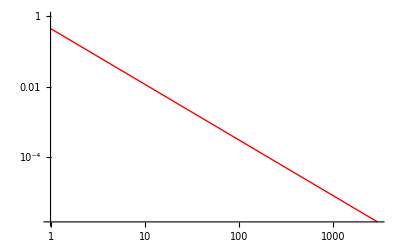

-Graphics-

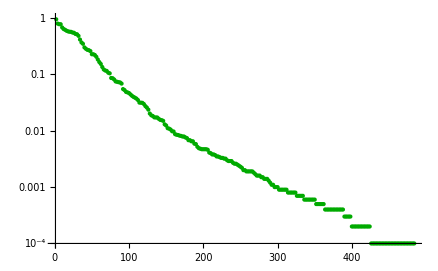

```mathematica
p4=ListLogPlot[d2/10000,PlotRange->{{1,Length[d2]},{0,1}},PlotStyle->{Thick,Darker[Green]}]
```

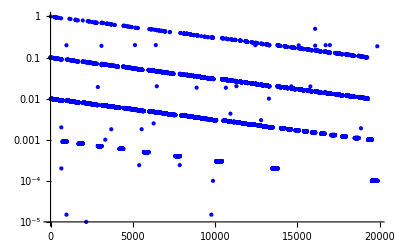

```mathematica
p2=ListLogPlot[zipfdata,PlotRange->{{1,Length[d]},{0,1}},PlotStyle->{Thick,Blue}]
```

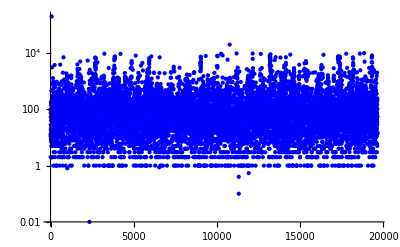

-Graphics-

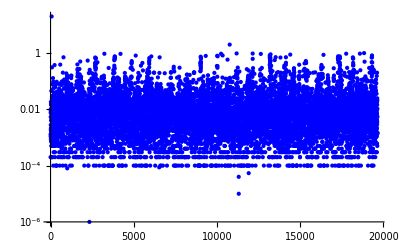

-Graphics-

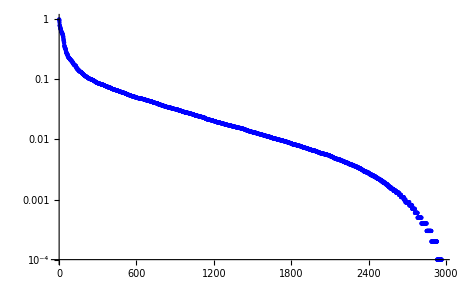

-Graphics-

```mathematica
Needs["PlotLegends`"]
```

```mathematica
Export["ChemistryAsALanguage.pdf",Show[p4,p2,Frame->True,FrameLabel->{"Rank","Frequency"},RotateLabel->True] ]
```

ChemistryAsALanguage.pdf

```mathematica
Export["English.pdf",p4]
```

English.pdf

```mathematica
Export["Chemistry.pdf",p2]
```

Chemistry.pdf

```mathematica
p3=LogPlot[1/x^{1/2},{x,1,Length[zipfdata]},PlotStyle->{Thick,Red}]
```

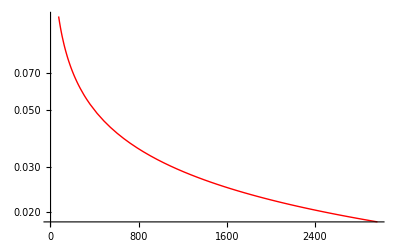

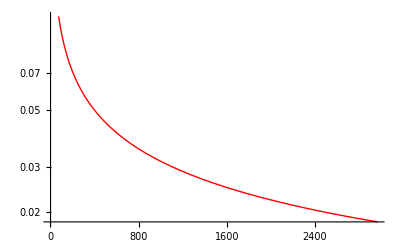

Show::gcomb: Could not combine the graphics objects in ….

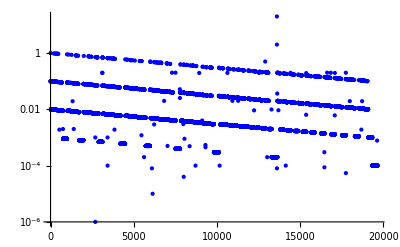
Show[-Graphics-,p3]

```mathematica
Show[p2,p3]
```

```mathematica
data=Import["/tmp/wars.csv"]⟦1;;All,2;;3⟧
```

{{D,4},{R,12},{R,3},{R,7},{R,5},{R,0},{R,1},{D,2},{R,4},{D,1},{R,11},{R,0},{R,1},{D,12},{R,0},{R,0},{R,0},{D,32},{D,5},{R,1},{D,0},{D,2},{R,0},{R,0},{D,0},{R,7},{R,5},{D,4},{R,9},{D,2}}

```mathematica
??If
```

If[condition,t,f] gives t if condition evaluates to True, and f if it evaluates to False. 
If[condition,t,f,u] gives u if condition evaluates to neither True nor False.

Attributes[If]={HoldRest,Protected}

```mathematica
Mean[(If[#1≠0,0,1]&)/@Select[data,#1⟦1⟧=="D"&]⟦1;;All,2⟧]//N
```

0.181818

```mathematica
Mean[(If[#1≠0,0,1]&)/@Select[data,#1⟦1⟧=="R"&]⟦1;;All,2⟧]//N
```

0.368421

```mathematica
(If[#1⟦1⟧=="D",{1,#1⟦2⟧},{0,#1⟦2⟧}]&)/@data
```

{{1,4},{0,12},{0,3},{0,7},{0,5},{0,0},{0,1},{1,2},{0,4},{1,1},{0,11},{0,0},{0,1},{1,12},{0,0},{0,0},{0,0},{1,32},{1,5},{0,1},{1,0},{1,2},{0,0},{0,0},{1,0},{0,7},{0,5},{1,4},{0,9},{1,2}}

```mathematica
Export["/tmp/peace.pdf",BarChart[{0.18181818181818182,0.3684210526315789}]]
```

/tmp/peace.pdf

```mathematica
Correlation[((If[#1⟦1⟧=="D",{0,#1⟦2⟧},{1,#1⟦2⟧}]&)/@data)⟦1;;All,1⟧,((If[#1⟦1⟧=="D",{0,#1⟦2⟧},{1,#1⟦2⟧}]&)/@data)⟦1;;All,2⟧]//N
```

-0.178886

```mathematica
??Correlation
```

Correlation[v_1,v_2] gives the correlation between the vectors v_1 and v_2.
Correlation[m] gives the correlation matrix for the matrix m.
Correlation[m_1,m_2] gives the correlation matrix for the matrices m_1 and m_2.
Correlation[dist] gives the correlation matrix for the multivariate symbolic distribution dist.
Correlation[dist,i,j] gives the (i,j)^th correlation for the multivariate symbolic distribution dist.

Attributes[Correlation]={Protected,ReadProtected}
 
Options[Correlation]={}